```mathematica
Quit
```

## Create the buttons at the top

```mathematica
Quit
```

```mathematica
With[{$pacletName="WeakCache", pid="JasonB"},
buttons=Row[{
Button["load "<>$pacletName<>" paclet",
$PublisherID;
$PublisherID=pid;
PacletDirectoryLoad[NotebookDirectory[]];
With[{syms=Join[Names[pid<>"`"<>$pacletName<>"`*"],Names[pid<>"`"<>$pacletName<>"`*`*"]]},(Unprotect[#];ClearAll[#];)&/@syms];
Get@(pid<>"`"<>$pacletName<>"`")
],
	Button["open resource definition notebook",NotebookOpen@FileNameJoin[{NotebookDirectory[],$pacletName,"ResourceDefinition.nb"}]
	]}
]];
SetOptions[EvaluationNotebook[],
DockedCells->Cell[BoxData[ToBoxes[buttons]],"DockedCell"]]
```

## Headline image

```mathematica
MoleculePlot[Molecule[…],ColorRules->{"C"->Directive[Black,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2}]
```

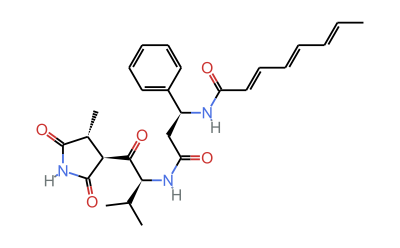
```mathematica
-Graphics-//shortInputForm
```

```mathematica
mplot=MoleculePlot[#,ColorRules->{("C"|"H")->Directive[Black,Thick],_->Directive[Red,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2},IncludeHydrogens->False]&;
SeedRandom[452];
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,17]]}],ImageSize->{325,275}]/.Tooltip->(#1&)
```

-Graphics-

```mathematica
mplot=MoleculePlot[#,ColorRules->{_->Directive[Black,Thick]},AtomLabels->None,Method->{"FontScaleFactor"->2}]&;
SeedRandom[45];
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,16]]}],ImageSize->{325,225}]/.Tooltip->(#1&)
```

```mathematica
SeedRandom[333];
mplot=MoleculePlot[#,ColorRules->{_->Directive[White,Thick]},AtomLabels->None]&
WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->mplot/@RandomSample[,20]]}],ImageSize->{300,200},Background->Darker@Gray]/.Tooltip->(#1&)
```

MoleculePlot[#1,ColorRules→{_→Directive[White,Thick]},AtomLabels→None]&

-Graphics-

```mathematica
SeedRandom[1234];Rasterize[WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->MoleculePlot/@RandomSample[,10]]}],ImageSize->300]]
```

-Graphics-

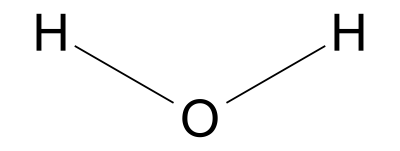

```mathematica
MoleculePlot["water",PlotTheme->"Monochrome"]
```

```mathematica
ImageIdentify[-Graphics-]
```

mathematical notation

## Tests

### Create tests

#### test writing function

```mathematica
Attributes[makeTest]={HoldRest};
makeTest[filename_,input_]:=With[{file=FileNameJoin[{NotebookDirectory[],"Tests",StringJoin[filename,If[StringEndsQ[filename,".mt"|".wlt"],"",".wlt"]]}]},
ResourceFunction["WriteUnitTest"][file,input]]
```

#### test-writing scratch

```mathematica
makeTest["TestCleanupAfter",Needs["JasonB`WeakCache`"]]
```

Adding test: TestCleanupAfter_20221024-YWV3YN

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

```mathematica
makeTest["TestCleanupAfter",Block[{expr=Range[5],expr2=5},
CleanupAfter[expr,expr2 *=2];
{expr2,CompoundExpression[Unset[expr],expr2]}
]]
```

Adding test: TestCleanupAfter_20221024-TLXPW5

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

```mathematica
makeTest["TestCleanupAfter",Block[{x},
{x=20,
Block[{expr=Range[5]},
CleanupAfter[expr,x *=2];
x
],
x}
]]
```

Adding test: TestCleanupAfter_20221024-TD3PHP

/Users/jasonb/WolframWorkspaces/Published_Paclets/WeakCache/Tests/TestCleanupAfter.wlt

### Run tests

```mathematica
Block[{testdir=FileNameJoin[{NotebookDirectory[],"Tests"}],testfiles},
testfiles=FileNames["*.mt"|"*.wlt",testdir];
With[{pacletDir=NotebookDirectory[],files=testfiles},PacletSymbol["MUnit","TestSuiteReport"][files,Initialization:>CompoundExpression[PacletDirectoryLoad[pacletDir]]]]
]
```

MUnit`TestSuiteReportObject[…]

## Scratch

```mathematica
$ContextPath
```

{WolframChemistry`IsomerGeneration`,DocumentationSearch`,ResourceLocator`,Init`,System`,Global`}

```mathematica
CountIsomers["C4H6O"]
```

{-d4,-c4}

54

```mathematica
CountIsomers["C4H6O"]//absoluteTiming
```

{21.762 ms,54}

```mathematica
CountIsomers["C8H12O2"]//absoluteTiming
```

{57.922 ms,245836}

```mathematica
CountIsomers["C14H24O2"]//absoluteTiming
```

{1 42.3128,1032393834}

```mathematica
res=GenerateIsomers["C510O","ExtraElements"->{{"Cf",2}}]
```

Failure[…]

```mathematica
res=GenerateIsomers["C3H6N","ExtraElements"->{{"Cf",2}}]
```

Failure[…]

```mathematica
res=GenerateIsomers["C6H11NO"]
```

IsomerResultObject[…]

```mathematica
strm=res["InputStream"]
```

InputStream[…]

```mathematica
Options[strm]
```

{BinaryFormat→False,Method→{File,BinaryFormat→False},AppendCheck→False}

```mathematica
Molecule["[CH5]"]
```

Molecule::valenc: Invalid valence for carbon atom at position 1.

Molecule[…]

```mathematica
Failure["blah",<|"MessageParameters"->{"foo"},"MessageTemplate"->Audio::nofile|>]
```

Failure[…]

```mathematica
FormatValues[InputStream]
```

{HoldPattern[MakeBoxes[ElisionsDump`stream:InputStream[BoxForm`name:_String|String,ElisionsDump`uid_Integer],BoxForm`fmt_]/;BoxForm`UseIcons&&Quiet[Options[ElisionsDump`stream]=!={}]]:>Module[{ElisionsDump`alwaysGrid,ElisionsDump`sometimesGrid,BoxForm`opts},BoxForm`opts=Options[ElisionsDump`stream];ElisionsDump`alwaysGrid={Name: ElisionsDump`clippedPane[FileNameTake[ToString[BoxForm`name],-1]],Unique ID: ElisionsDump`uid};ElisionsDump`sometimesGrid={Name: ElisionsDump`expandablePane[BoxForm`name],Unique ID: ElisionsDump`uid,Binary: BinaryFormat/.BoxForm`opts,Open: };BoxForm`ArrangeSummaryBox[InputStream,ElisionsDump`stream,BoxForm`GenericIcon[InputStream],ElisionsDump`alwaysGrid,ElisionsDump`sometimesGrid,BoxForm`fmt,CompleteReplacement→True]]}

```mathematica
Options[res]
```

{}

```mathematica
res["InputStream"]
```

InputStream[…]

InputStream[…]

```mathematica
Quit
```

```mathematica
InputStream[…]//Options
```

{}

```mathematica
pd@InputStream
```

```mathematica
Inactive[Power][2,3]//TraditionalForm
```

2^3

```mathematica
Inactive[Power][2,x]
```

2^x

```mathematica
Power[2,x]
```

2^x

```mathematica
FullForm[%]
```

Power[2,x]

```mathematica
?
```

```mathematica
ReadList@%
```

Set::wrsym: Symbol C is Protected.

Set::wrsym: Symbol O is Protected.

ReadList::readt: Invalid input found when reading O=CC(=C)C(C)(N)C
 from /Users/jasonb/Documents/Wolfram/IsomerGeneration/C6H11NO_ded713bb-edef-459f-833f-04e2c5943375/C6H11NO.smi.

{C^5 N,$Failed}

```mathematica
ProcessStatus@res
```

Running

```mathematica
KillProcess@res
```

```mathematica
DeleteFile@res
```

```mathematica
$TemporaryDirectory
```

```mathematica
res
```

```mathematica
$IsomerOutputDirectory
```

```mathematica
GenerateIsomers["C3H6U","ExtraElements"->{{"U",4}}]
```

IsomerResultObject[…]

```mathematica
%9["SMILES"]
```

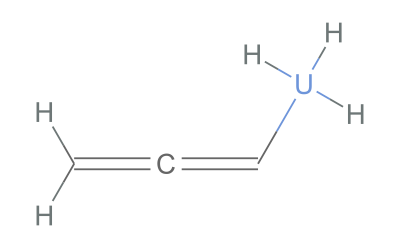
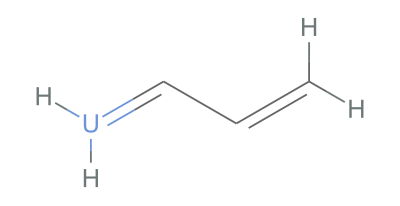
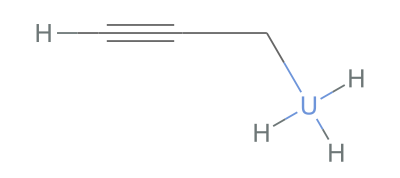
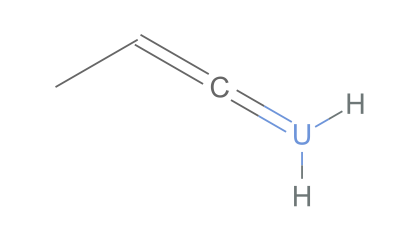
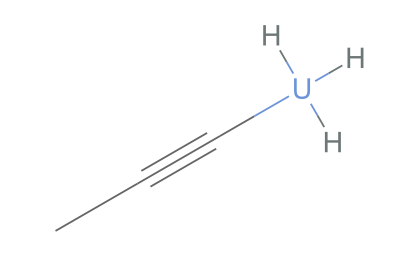
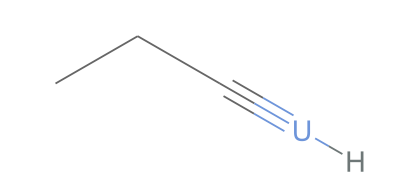
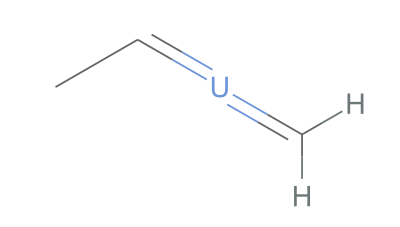
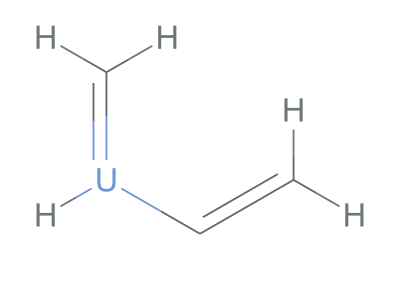

```mathematica
MoleculePlot/@{"C=C=C[UH3]","C=CC=[UH2]","C#CC[UH3]","CC=C=[UH2]","CC#C[UH3]","CCC#[UH]","C=[U]=CC","C=[UH]C=C","C#[U]CC","C[UH]=C=C","C[U]#CC","C[UH2]C#C","[UH3]C1=CC1","[UH2]=C1CC1","[UH3]C1C=C1","CC1=[UH]C1","C=C1[UH2]C1","CC=1[UH2]C1","CC1[UH]=C1","C[U]1=CC1","C=[U]1CC1","C[UH]1C=C1","C1[UH]=CC1","C1[UH2]C=C1","C1C2C1[UH2]2","C1[UH]2C1C2"}
```

```mathematica
GenerateIsomers["C12H21NO"]
```

```mathematica
KillProcess
ProcessStatus
Read
```

```mathematica
Read[iro,"Molecule"]
```

```mathematica
First@%
```

<|GeneratedDirectory→True,Method→surge,OutputDirectory→/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H6U_489550a3-4659-41e4-b5b0-9b5d5d4deed1,Formula→C3H6U,CommandLine→{-o/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H6U_489550a3-4659-41e4-b5b0-9b5d5d4deed1/C3H6U.smi,-S,-d4,-c4,-EU4,C3H6U},Process→ProcessObject[…],IsomerCount→26|>

```mathematica
MoleculePlot/
```

```mathematica
StringCases[{"C3UH9  H=9 C=3 U=1  nv=4 edges=3-3 DBE=0 maxd=4 maxc=4",">Z wrote 2 -> 4 -> 4 in 0.00 sec"},]
```

```mathematica
res=GenerateIsomers["C13H21AzO","Part"->"8/9","ExtraElements"->{{"U",3},{"Z","U",5}(*{"Az","As",5}*)}]
```

IsomerResultObject[…]

```mathematica
%
```

IsomerResultObject[…]

```mathematica
KillProcess@%
```

```mathematica
KillProcess@%59
```

```mathematica
stream=OpenRead[%59["FileName"]]
```

InputStream[…]

```mathematica
Skip[stream,String,904895]
```

```mathematica
MoleculePlot3D[ReadLine[stream]]&/@Range[5]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
RandomSample[%["SMILES"],5]
```

{CC(=C)[U]=[UH3],C[UH]#C[UH]C,[UH2]C1[UH](=C)C1,[UH3]=C=CC[UH2],[UH2][UH2]=C1CC1}

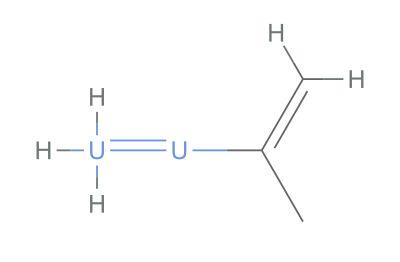
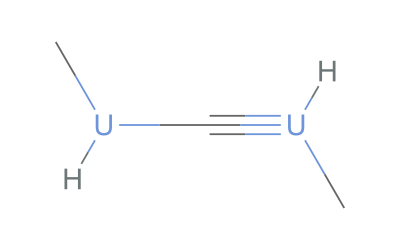
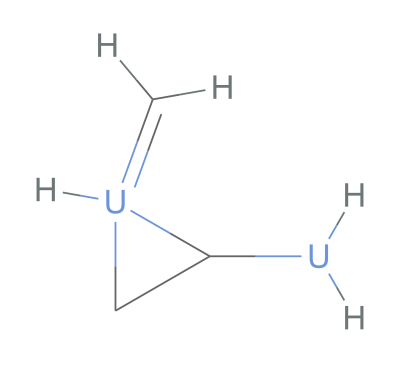
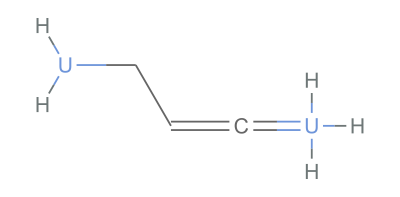
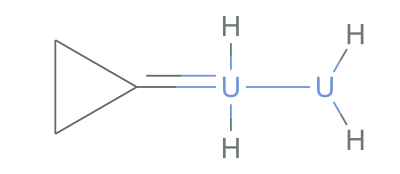

```mathematica
MoleculePlot/@%
```

```mathematica
Keys@First@%
```

{GeneratedDirectory,Method,OutputDirectory,Formula,CommandLine,Process,IsomerCount}

```mathematica
Keys@%
```

{GeneratedDirectory,Method,OutputDirectory,Formula,CommandLine,Process}

```mathematica
FileExistsQ@%
```

False

```mathematica
ReadList[res["Process"]["StandardError"],String]
```

ReadList::openx: InputStream[/Users/jasonb/Library/Mathematica/ApplicationData/ProcessLink/Streams/wl-stream-stderr-19o1bjjpyu3sm,4] is not open.

ReadList[InputStream[/Users/jasonb/Library/Mathematica/ApplicationData/ProcessLink/Streams/wl-stream-stderr-19o1bjjpyu3sm,4],String]

```mathematica
Close[res["Process"]["StandardOutput"]]
```

/Users/jasonb/Library/Mathematica/ApplicationData/ProcessLink/Streams/wl-stream-stdout-19o1bjjpyu3sm

```mathematica
res=GenerateIsomers["CxCfC4H7F2","ExtraElements"->{{"Cf",2},{"Cx","Cf",3}}]
```

{-d4,-c4,-ECf2,-ECxCf3}

IsomerResultObject[…]

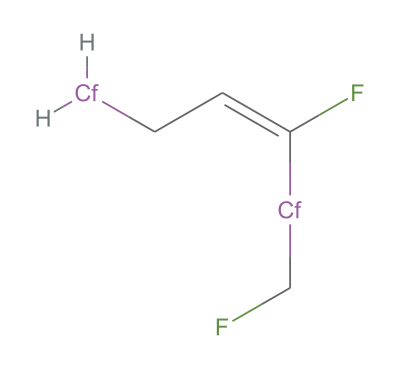
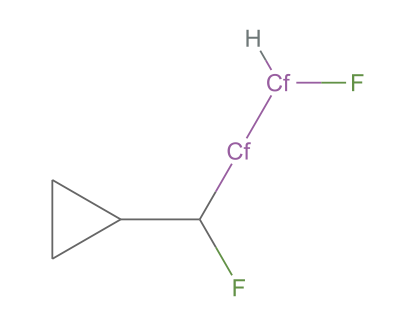
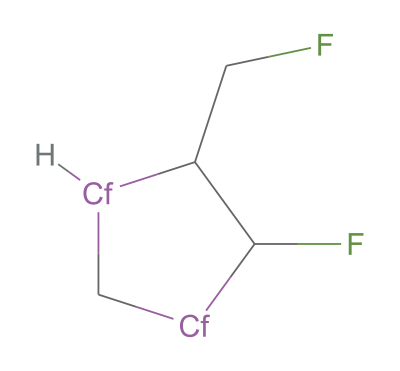
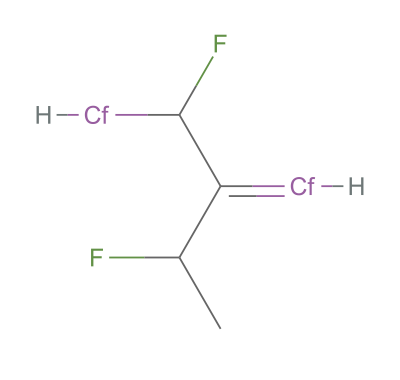
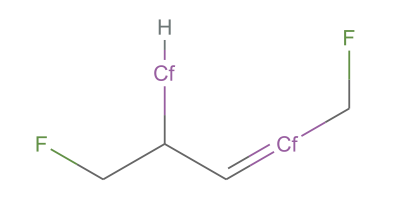

```mathematica
MoleculePlot/@RandomSample[res["SMILES"],5]
```

```mathematica
(res=GenerateIsomers["Cf4H8F2"];
ProcessStatus[res["Process"]])//absoluteTiming
```

{13.426 ms,Finished}

```mathematica
res=GenerateIsomers["Cf4H8F2"];
ProcessStatus[res["Process"]]//absoluteTiming
```

{167. μs,Finished}

```mathematica
pf@Failure["InvalidFormula",<|"MessageTemplate"->"Invalid formula `1`.","MessageParameters"->{"Cf2"}|>]
```

```mathematica
Failure["InvalidFormula",
	<|"MessageTemplate" -> "Invalid formula `1`.", "MessageParameters" -> {"Cf2"}|>
]
```

```mathematica
Options[StartProcess]
```

{ProcessDirectory→Inherited,ProcessEnvironment→Inherited}

```mathematica
res["Process"]["Properties"]
```

{Program,UID,PID,PPID,User,Path,Memory,Threads,StartTime,UserTime,SystemTime,RealTime,Dataset,StandardInput,StandardOutput,StandardError}

```mathematica
res["Process"]["StandardError"]
```

InputStream[…]

```mathematica
ReadLine@res["Process"]["StandardError"]
```

>E surge : unknown element name

```mathematica
ReadLine@%%
```

EndOfFile

```mathematica
%
```

IsomerResultObject[…]

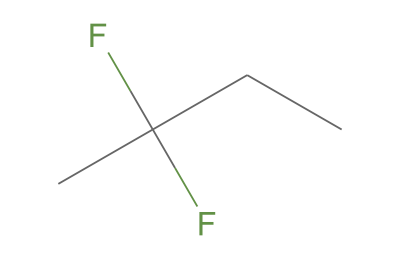
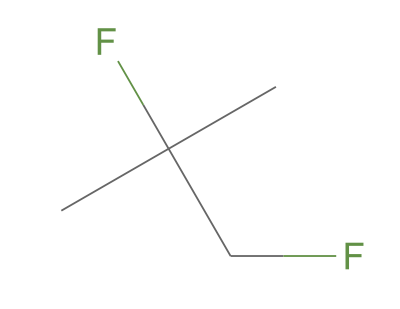
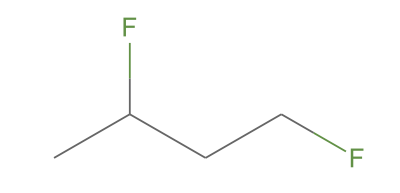
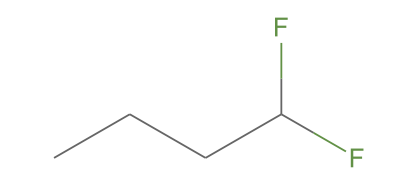
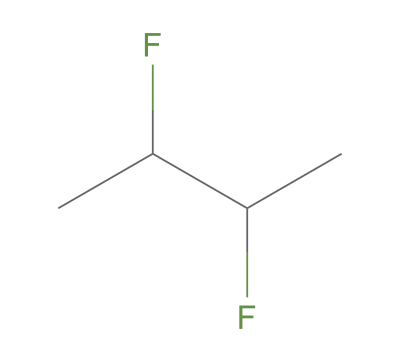
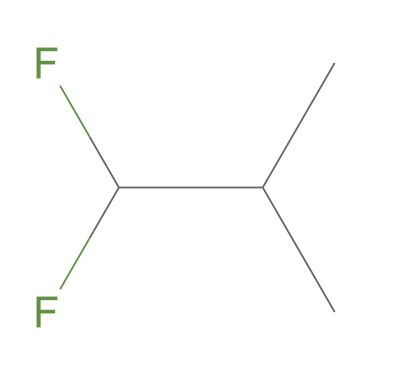
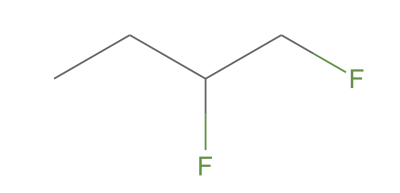
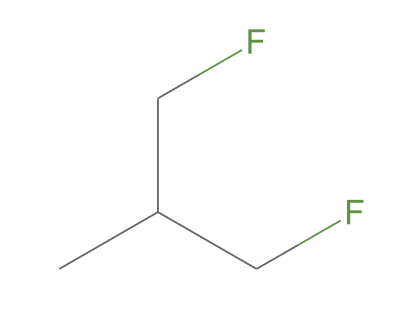

```mathematica
MoleculePlot/@%["SMILES"]
```

```mathematica
pd@igp`addExtraElements
```

```mathematica
ClearAll["igp`*"]
```

```mathematica
igp`addExtraElements[f,None]
```

WolframChemistryTeam`IsomerGeneration`Private`addExtraElements[f,None]

```mathematica
pf@FilterRules[Options[GenerateIsomers],Except[GeneratedAssetLocation|Asynchronous|"Part"|Method]]
```

```mathematica
FilterRules[Options @ WolframChemistryTeam`IsomerGeneration`GenerateIsomersGenerateIsomers,
	Except[GeneratedAssetLocation|Asynchronous|"Part"|Method]
]
```

```mathematica
Options[GenerateIsomers]={GeneratedAssetLocation:>Automatic,Asynchronous->True,"BondCount"->Automatic,"Length3CycleCount"->Automatic,"Length4CycleCount"->Automatic,"Length5CycleCount"->Automatic,"DisallowOddLengthCycles"->False,"DisallowTripleBonds"->False,"RequirePlanarity"->False,"MaxDegree"->4,"MaxCoordinationNumber"->4,"ForbiddenSubstructures"->None,"ExtraCommands"->{},"Part"->All,"ExtraElements"->None,Method->Automatic}
```

```mathematica
CountIsomers["C4H6O"]
```

{/Users/jasonb/WolframWorkspaces/Published_Paclets/IsomerGeneration/IsomerGeneration/surge/MacOSX-x86-64/surge-macos-v1.0,-u,-d4,-c4,C4H6O}

<|ExitCode→0,StandardOutput→,StandardError→C4OH6  H=6 C=4 O=1  nv=5 edges=4-6 DBE=2 maxd=4 maxc=4
>Z generated 12 -> 25 -> 54 in 0.00 sec
|>

```mathematica
res=GenerateIsomers["C4H6O"]
```

IsomerResultObject[…]

```mathematica
RunProcess[{igp`$surge,"-u","Cf5H10O2","-o/Users/jasonb/Documents/Wolfram/IsomerGeneration/count"}]
```

<|ExitCode→1,StandardOutput→,StandardError→>E surge : unknown element name
|>

```mathematica
{Lookup[%67,"ExitCode"]}
```

{1}

```mathematica
{Lookup[%67,"ExitCodee",Sequence@@{}]}
```

{}

```mathematica
addExtraElements[ds_,extraElements:{(_List|_Association)...}]
```

```mathematica
ElementData["Cf"]
```

```mathematica
Surge["C4H6O",Asynchronous->False]
```

{CC(=O)C=C,C=C(O)C=C,CC(O)=C=C,CC(O)C#C,CC(=C)C=O,CC(C)=C=O,CC1(O)C=C1,C=C1OCC1,CC=1OCC1,CC1OC=C1,O=C1CCC1,OC1=CCC1,OC1C=CC1,C=C1COC1,CC1=COC1,CC1=C(C)O1,CC1C(=C)O1,CC1=C(O)C1,CC1C(=O)C1,CC1C(O)=C1,C=C1C(O)C1,CC=1C(O)C1,CC12C(C2)O1,OC12C(C2)C1,C=C=COC,CC#COC,C#CCOC,CC=C=CO,CCC=C=O,C=CC=CO,CCC#CO,CC=CC=O,C=C=CCO,CC#CCO,C=CCC=O,C#CCCO,C=COC=C,CCOC#C,COC1=CC1,COC1C=C1,CC=C1OC1,CCC=1OC1,C=CC1OC1,OCC1=CC1,OC=C1CC1,O=CC1CC1,OCC1C=C1,C1C2(C1)OC2,C1C=COC1,C1=CCOC1,C12C(CC1)O2,C12C(CO1)C2,OC1C2CC12,CC1C2OC12}

```mathematica
Surge["C8H13O2N","ExtraCommands"->{"-m1/9"}]
```

IsomerResultObject[…]

```mathematica
list1=Surge["C8H13O2N","ExtraCommands"->{"-m"<>IntegerString[#]<>"/9"}]&/@Range[0,8];
```

```mathematica
Length[#["SMILES"]]&/@list1
```

{128167,253089,388073,687355,981619,1817275,1720912,1143732,214071}

```mathematica
Total[Echo@(Length[#["SMILES"]]&/@list1)]
```

{128167,253089,388073,687355,981619,1817275,1720912,1143732,214071}

7334293

```mathematica
list1
```

```mathematica
Surge["C8H13O2N","ExtraCommands"->{"-m"<>IntegerString[2]<>"/9"}]
```

IsomerResultObject[…]

```mathematica
Surge["C8H13O2N","ExtraCommands"->{"-m"<>IntegerString[2]<>"/22"}]
```

IsomerResultObject[…]

```mathematica
%53
```

IsomerResultObject[…]

```mathematica
DeleteFile/@%
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
res=Surge["C8H13O2N"]
```

IsomerResultObject[…]

```mathematica
ProcessStatus@%
```

Finished

```mathematica
ff=Failure["InvalidFormula",<|"MessageTemplate"->"Invalid formula `1`.","MessageParameters"->{"Cf2"}|>];
```

```mathematica
func[x_]:=Enclose@Module[{var},
var=Confirm[ff,"bad"];
3x+var
]
```

```mathematica
func[2]
```

Failure[…]

```mathematica
res
```

IsomerResultObject[…]

```mathematica
Total@%
```

7334293

```mathematica
DeleteFile/@list1
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Leng
```

```mathematica
%23
```

$Aborted

```mathematica
ProcessStatus@%23
```

Running

```mathematica
KillProcess@%23
```

```mathematica
FileSize@%23["FileName"]
```

8.41185 GB

```mathematica
%23["FileName"]
```

/Users/jasonb/Documents/Wolfram/IsomerGeneration/a4443017-8713-4389-8d00-5e6a10795cd8/C16H23O2N.smi

```mathematica
MoleculePlot3D/@
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{%,%%,%%%,%%%%,%%%%%}
```

{IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],11087912,{602370,610461,138137,458291,592666,2568420,289376,1226940,83467,2659553,1858231,0}}

```mathematica
DeleteFile/@%[[;;3]]
```

{Null,Null,$Failed}

```mathematica
%
```

IsomerResultObject[…]

```mathematica
list1=Surge["C10H17ON","ExtraCommands"->{"-m"<>IntegerString[#]<>"/12"}]&/@Range[12]
```

{IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…],IsomerResultObject[…]}

```mathematica
DeleteFile/@list1
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Length[#["SMILES"]]&/@list1
```

{602370,610461,138137,458291,592666,2568420,289376,1226940,83467,2659553,1858231,0}

```mathematica
Total@%
```

11087912

```mathematica
iro=MayGen["C4H6O"]
```

IsomerResultObject[…]

```mathematica
iro["IsomerCount"]
```

265782

```mathematica
iro
```

IsomerResultObject[…]

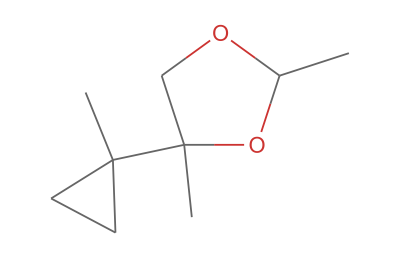
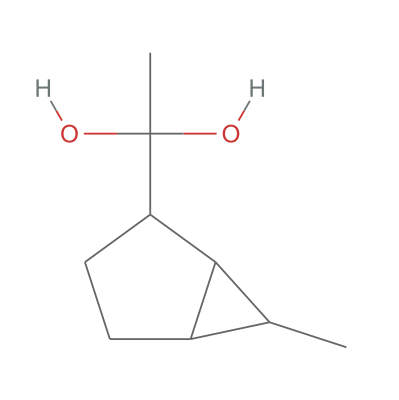
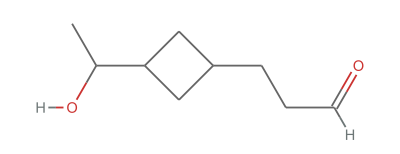
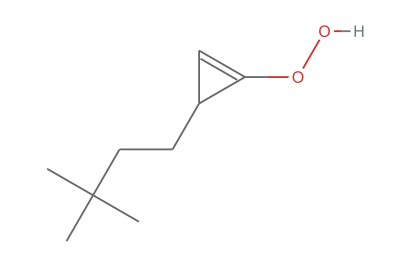
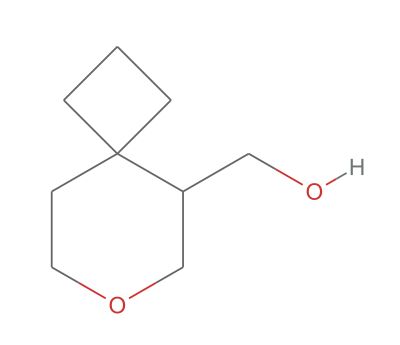
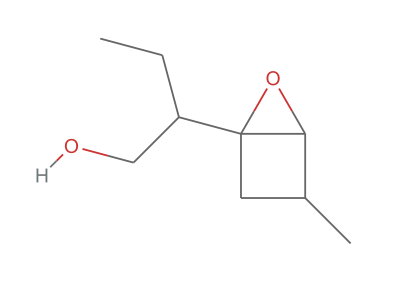
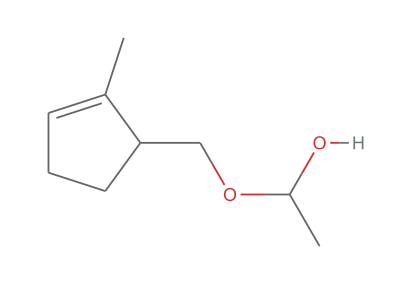
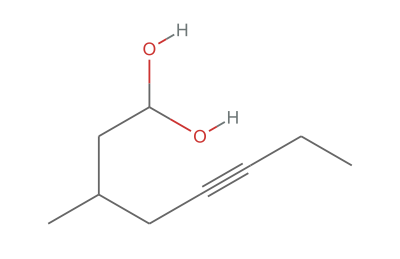

```mathematica
MoleculePlot/@RandomSample[iro["SMILES"],15]
```

```mathematica
KillProcess@iro
```

```mathematica
"C9H16O2"
```

```mathematica
iro["SMILES"]
```

{NC1(N)CC1,C=C(N)CN,NC=C(N)C,NC(N)=CC,NC=CCN,C=CC(N)N,NC1CC1N,C=C(NN)C,N=C(N)CC,N=C(C)CN,NC1(NC1)C,C=C(N)NC,NNC1CC1,C=CCNN,N=CCCN,NC1NCC1,C=CNCN,NCC1NC1,NC1CNC1,NNC=CC,NC=CNC,N=CC(N)C,NC1NC1C,N(N)=C(C)C,N(=C(N)C)C,NN1CCC1,N(=C)CCN,NCN1CC1,N(N)=CCC,NN1CC1C,C=CN(N)C,N(=CN)CC,N(=CC)CN,N(=CCN)C,N(=C)C(N)C,NC1N(C)C1,N=C(NC)C,N1NC1(C)C,N1NCCC1,N1CNCC1,C=CNNC,N1NC(C)C1,N=CCNC,N1NC1CC,N(C)C1NC1,N1CNC1C,N=CNCC,N=NCCC,N1N(C)CC1,N(=C)NCC,N(N1CC1)C,N1N(C1)CC,N1CN(C)C1,N(=C)CNC,N=NC(C)C,N(=CC)NC,N1N(C)C1C,N(=CNC)C,N=CN(C)C,N(=C)N(C)C,N1(N(C)C1)C,N(=NCC)C}

```mathematica
iro["FileName"]
```

/private/var/folders/yy/3fh5ypq11nx5032xgf6xy36w000_6y/T/6f28110d-0dad-476c-8402-0f359b63684a/C3OH8.smi

```mathematica
FileExistsQ@%17
```

False

```mathematica
DeleteFile@iro
```

```mathematica
%6
```

IsomerResultObject[…]

```mathematica
%6["FileName"]
```

/private/var/folders/yy/3fh5ypq11nx5032xgf6xy36w000_6y/T/fefba244-a82e-43e3-80ac-e1e66dad7482/C3OH8.smi

```mathematica
FileExistsQ@%
```

True

```mathematica
DeleteFile@%6
```

$Failed

```mathematica
%6["SMILES"]
```

{OCCC,OC(C)C,O(C)CC}

```mathematica
ChemicalFormula@*Molecule/@%
```

{C_3H_8O,C_3H_8O,C_3H_8O}

```mathematica
%["IsomerCount"]
```

2

```mathematica
%
```

```mathematica
IsomerResultObject[…]//DeleteFile
```

$Failed

```mathematica
%["FileName"]
```

/private/var/folders/yy/3fh5ypq11nx5032xgf6xy36w000_6y/T/1105443d-6a00-4aa8-8b28-26a68807cded/C2OH6.smi

```mathematica
FileExistsQ@%
```

True

```mathematica
%3["SMILES"]
```

{OCC,O(C)C}

```mathematica
DeleteFile@%4
```

```mathematica
DeleteDirectory@DirectoryName@%4
```

```mathematica
First@%
```

<|Formula→C2OH4,Process→ProcessObject[…],OutputDirectory→/Users/jasonb|>

```mathematica
%12["SMILES"]
```

/Users/jasonb/C2OH4.smi

```mathematica
FileExistsQ@%
```

```mathematica
%4["OutputDirectory"]//DirectoryQ
```

False

```mathematica
FileExistsQ@%
```

False

```mathematica
ProcessStatus@%4
```

Finished

```mathematica
$paclet=PacletObject["WolframChemistry/IsomerGeneration"];
```

```mathematica
$java=FileNameJoin[{$InstallationDirectory,"SystemFiles","Java",$SystemID,"bin","java"}];
$MAYGEN=$paclet["AssetLocation","MAYGEN"];
```

```mathematica
outputDir=FileNameJoin[{$UserDocumentsDirectory,"Wolfram","IsomerGeneration"}];
If[!DirectoryQ[outputDir],CreateDirectory@outputDir]
```

```mathematica
uuid=CreateUUID["C2OH4_"];
```

C2OH4_4e3b9a55-d50a-4c80-a7da-bd3d4d0a2354

```mathematica
InstallJava[]
```

LinkObject[…]

```mathematica
ProcessStatus[process]
```

Finished

```mathematica
resultPattern[data_]:=HoldPattern[IsomerResultObject[data]/;AssociationQ[data]]
```

```mathematica
Molecule/@ImportString["OC=C
O1CC1
O=CC","Lines"]
```

{Molecule[…],Molecule[…],Molecule[…]}

```mathematica
ReadList
```

```mathematica
First@%
```

'/Applications/KernelBank01.app/Contents/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JLink' -Xmx512m  com.wolfram.jlink.Install -init "/private/var/folders/yy/3fh5ypq11nx5032xgf6xy36w000_6y/T/m000002756621"

```mathematica
Needs["JLink`"]
```

```mathematica
InstallJava[]
```

LinkObject[…]

```mathematica
process=StartProcess[{"java","-jar",$MAYGEN,"-f","C22O2H40","-v","-t","-o",FileNameJoin[{outputDir,uuid}]}]
```

```mathematica
ProcessObject[…]//ProcessStatus
```

Finished

```mathematica
Options[InstallJava]
```

{ClassPath→Automatic,CommandLine→Automatic,JVMArguments→None,ForceLaunch→False,Default→Automatic,CreateExtraLinks→Automatic,Asynchronous→Automatic}

```mathematica
Environment["WRI_JAVA_HOME"]
```

$Failed

```mathematica
JLink`InstallJava`Private`createCommandLine[Automatic,{}]
```

'/Applications/KernelBank01.app/Contents/SystemFiles/Links/JLink/JLink.app/Contents/MacOS/JLink' -Xmx512m  com.wolfram.jlink.Install

```mathematica
RunProcess[{FileNameJoin[{$InstallationDirectory,"SystemFiles","Java",$SystemID,"bin","java"}]
```

```mathematica
R
```

/Applications/KernelBank01.app/Contents/SystemFiles/Java/MacOSX-x86-64/bin/java

```mathematica
FileExistsQ@%
```

True

```mathematica
KillProcess@process
```

```mathematica
FileNameJoin[{outputDir,uuid}]
```

/Users/jasonb/Documents/Wolfram/IsomerGeneration/C2OH4_b9e9a0ab-2250-42b9-aa33-38c56e81bc14

```mathematica
process["Properties"]
```

{Program,UID,PID,PPID,User,Path,Memory,Threads,StartTime,UserTime,SystemTime,RealTime,Dataset,StandardInput,StandardOutput,StandardError}

```mathematica
process["StandardOutput"]
```

InputStream[…]

```mathematica
Read@%%%%
```

Time:0.015 seconds

```mathematica
ProcessStatus[process]
```

Running

```mathematica
process["Dataset"]
```

```mathematica
ReadLine[process]
```

$Aborted

```mathematica
$TemporaryDirectory
```

/private/var/folders/yy/3fh5ypq11nx5032xgf6xy36w000_6y/T

```mathematica
CreateDirectory
```

```mathematica
$paclet["AssetLocation","surge"]
```

/Users/jasonb/WolframWorkspaces/Published_Paclets/IsomerGeneration/IsomerGeneration/surge/MacOSX-x86-64/surge-macos-v1.0

```mathematica
FileExistsQ@%
```

True

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
Block[{$SystemID="Linux-x86-64"},$paclet["AssetLocation","surge"]]
```

Block::lockt: Cannot localize locked symbol $SystemID in assignment $SystemID=Linux-x86-64 from local variable specification {$SystemID=Linux-x86-64}.

Block[{$SystemID=Linux-x86-64},$paclet[AssetLocation,surge]]

```mathematica
RunProcess[{"/Users/jasonb/Downloads/surge-macos-v1.0","-help"}]
```

RunProcess::pnfd: Program /Users/jasonb/Downloads/surge-macos-v1.0 not found.  Check Environment["PATH"].

$Failed

```mathematica
Divide[ChemicalInstance[ChemicalFormula[{"Cl"->2},<|"Phase"->"Gas"|>],<|"Volume"->Quantity[(Around[500.,0.5]),"Milliliters"],"Density"->Quantity[0.003214,("Grams")/("Centimeters")^3]|>],10]
```

ChemicalInstance[Cl_2(g),<|Volume→(50.000.05) mL,Density→0.003214 g/cm^3|>]

text f[x]

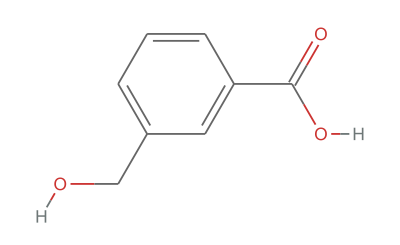

```mathematica
MoleculePlot@"OC(C1=CC(CO)=CC=C1)=O"
```

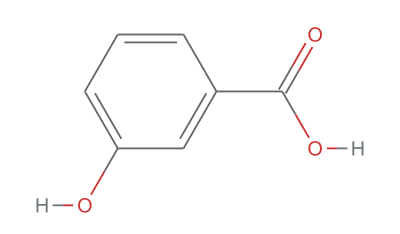

```mathematica
MoleculePlot@"OC(C1=CC(O)=CC=C1)=O"
```

```mathematica
Molecule["benzene"]["BondWeightedAdjacencyMatrix",IncludeHydrogens->False]//MatrixForm
```

(0. | 1.5 | 0. | 0. | 0. | 1.5
1.5 | 0. | 1.5 | 0. | 0. | 0.
0. | 1.5 | 0. | 1.5 | 0. | 0.
0. | 0. | 1.5 | 0. | 1.5 | 0.
0. | 0. | 0. | 1.5 | 0. | 1.5
1.5 | 0. | 0. | 0. | 1.5 | 0.)

```mathematica
Molecule["benzene"]["BondOrder"]
```

{1.5,1.5,1.5,1.5,1.5,1.5,1.,1.,1.,1.,1.,1.}

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`callMayGen["-f","C2OH6","-smi","-o","/Users/jasonb/Documents/Wolfram/IsomerGeneration"]
```

ProcessObject[…]

```mathematica
RunProcess[{"java","-jar",PacletObject["WolframChemistry/IsomerGeneration"]["AssetLocation","MAYGEN"],"-f","C2OH6","-smi","-o","/Users/jasonb/Documents/Wolfram/IsomerGeneration"}]
```

<|ExitCode→0,StandardOutput→,StandardError→|>

```mathematica
FilePrint["/Users/jasonb/Documents/Wolfram/IsomerGeneration/C2OH6.smi"]
```

OCC
O(C)C

```mathematica
ProcessStatus@%
```

Finished

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`$MAYGEN
```

```mathematica
PacletObject["WolframChemistry/IsomerGeneration"]["AssetLocation","MAYGEN"]
```

/Users/jasonb/WolframWorkspaces/Published_Paclets/IsomerGeneration/IsomerGeneration/MayGen/MAYGEN-1.8.jar

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`$surge
```

/Users/jasonb/WolframWorkspaces/Published_Paclets/IsomerGeneration/IsomerGeneration/surge/MacOSX-x86-64/surge-macos-v1.0

```mathematica
RunProcess[{WolframChemistryTeam`IsomerGeneration`Private`$surge,"-u","C10H16O"}]
```

<|ExitCode→0,StandardOutput→,StandardError→C10OH16  H=16 C=10 O=1  nv=11 edges=10-13 DBE=3 maxd=4 maxc=4
>Z generated 22674 -> 125754 -> 437881 in 0.09 sec
|>

```mathematica
ChemicalFormula["C10H16O"]["FormulaDisplay"]
```

C_10H_16O

```mathematica
MayGen["C10H16O"]
```

IsomerResultObject[…]

```mathematica
isomers=%
```

IsomerResultObject[…]

```mathematica
DeleteFile@isomers
```

```mathematica
isomers
```

```mathematica
Names["*`*FormulaQ"]
```

{Chemistry`Reactions`ChemicalFormulaQ}

```mathematica
RandomChoice[isomers["SMILES"],8]
```

{O1CC(=CC1CC=C(C)C)C,O1C(=CC)C2CC(C1)CC2C,O=C1C(C)C1CCC2CC2C,O(C)C1C2CC3CC1(CC)C32,O1C=CCCCC1(C=C)CC,O1CCC12CC2C3(C)CCC3,O(C=C)C1C=C(C)C1C(C)C,OC1C=C2CCCC2C1(C)C}

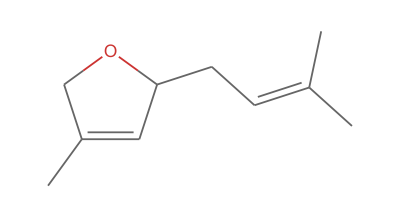
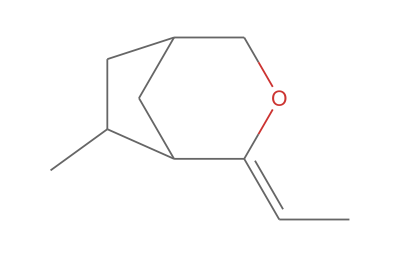
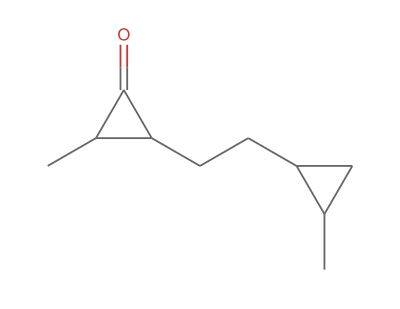
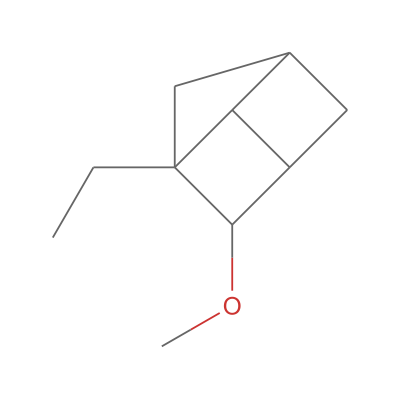
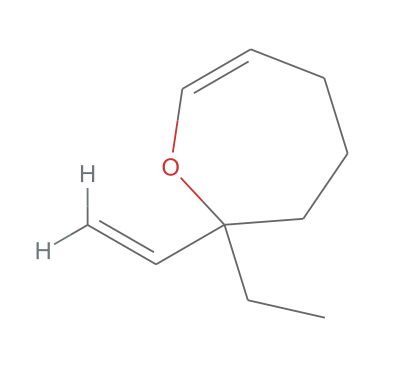
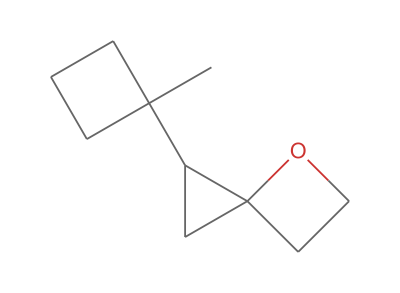
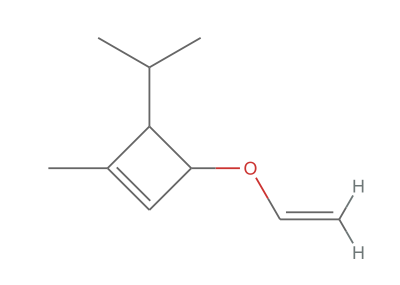
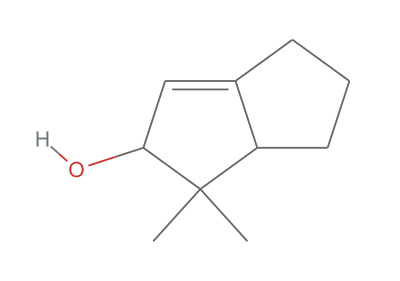

```mathematica
MoleculePlot/@%
```

```mathematica
files1=Surge["C8H13O2N","ExtraCommands"->{"-m"<>IntegerString[#]<>"/22"}]&/@Range[0,10];
```

```mathematica
ProcessStatus/@files1
```

{Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished}

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`lineCount[#["FileName"]]&/@files1
```

{0,95279,362160,67206,908682,800262,1749215,24954,0,1474,0}

```mathematica
files2=Surge["C8H13O2N","ExtraCommands"->{"-m"<>IntegerString[#]<>"/22"}]&/@Range[11,21];
```

```mathematica
ProcessStatus/@files2
```

{Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished,Finished}

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`lineCount[#["FileName"]]&/@files2
```

{24920,654442,71485,1011195,0,1062983,223398,117140,146292,0,13206}

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`lineCount[#["FileName"]]&/@Join[files1,files2]
```

{0,95279,362160,67206,908682,800262,1749215,24954,0,1474,0,24920,654442,71485,1011195,0,1062983,223398,117140,146292,0,13206}

```mathematica
Total@%
```

7334293

```mathematica
fil0=Surge["C8H17O2N"]
```

IsomerResultObject[…]

```mathematica
fil0
```

IsomerResultObject[…]

```mathematica
Import["/Users/jasonb/Documents/Wolfram/IsomerGeneration/37e91309-8323-4488-9cba-e0e2a1beec88/C8H13O2N.smi","MoleculeCount"]//absoluteTiming
```

{1.14791 s,7334293}

```mathematica
res=Import["/Users/jasonb/Documents/Wolfram/IsomerGeneration/2c7544d4-533a-4628-be6d-cb35dab3df23/C8H17O2N.smi",{"MoleculeCount"}]//absoluteTiming
```

{66.512 ms,301851}

```mathematica
Length@res
```

101

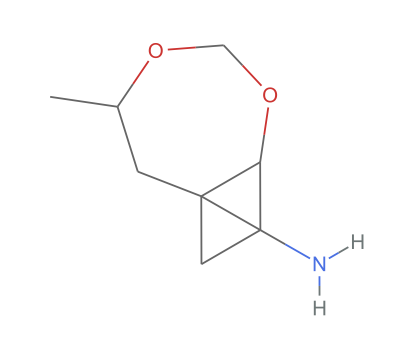
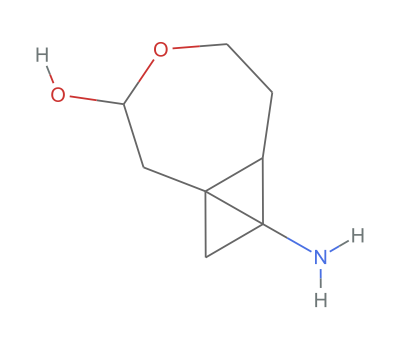
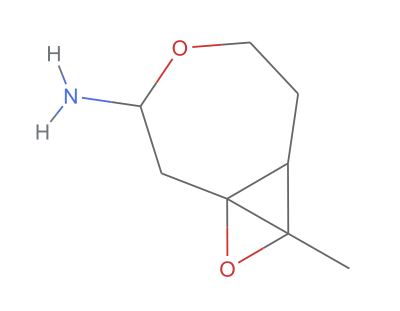
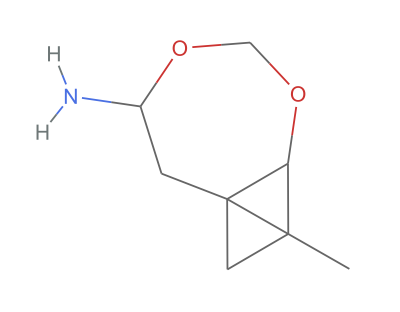
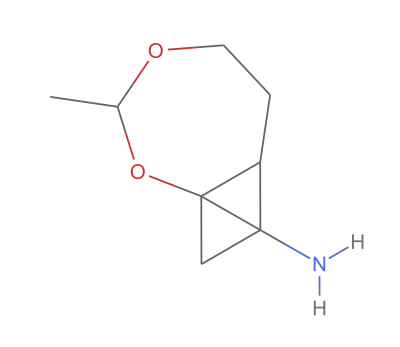

```mathematica
MoleculePlot/@RandomSample[res,5]
```

```mathematica
ProcessStatus@%
```

Finished

```mathematica
list1=Surge["C6H7NO",Asynchronous->False];//absoluteTiming
```

{117.041 ms,Null}

```mathematica
list2=Surge["C6H7NO",Asynchronous->False,"DisallowOddLengthCycles"->True];//absoluteTiming
```

{84.491 ms,Null}

```mathematica
list3=Surge["C16H22N2O"];//absoluteTiming
```

{18.832 ms,Null}

```mathematica
list3
```

IsomerResultObject[…]

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`lineCount[list3["FileName"]]//absoluteTiming
```

{1 11.8436,604902215}

```mathematica
stream=OpenRead[list3["FileName"]]
```

InputStream[…]

```mathematica
Table[Molecule[ReadLine[stream]],5]
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
Close@stream
```

/Users/jasonb/Documents/Wolfram/IsomerGeneration/89708d83-2e86-4626-a2d6-4a505a161e09/C16H22N2O.smi

```mathematica
({Iconize[#],FileSize[#]}&/@FileNames["*.smi","/Users/jasonb/Documents/Wolfram/IsomerGeneration",Infinity])//SortBy[Last]
```

{{,0. B},{,0. B},{,0. B},{,0. B},{,0. B},{,0. B},{,10. B},{,28.264 kB},{,250.931 kB},{,0.508423 MB},{,0.53112 MB},{,0.551739 MB},{,1.369 MB},{,1.51894 MB},{,2.08118 MB},{,2.39923 MB},{,2.70426 MB},{,4.55167 MB},{,5.55502 MB},{,7.9767 MB},{,7.9767 MB},{,8.50481 MB},{,9.49564 MB},{,13.1155 MB},{,16.5043 MB},{,19.4639 MB},{,20.7952 MB},{,20.9616 MB},{,36.8534 MB},{,151.634 MB},{,151.634 MB},{,8.41185 GB}}

/Users/jasonb/Documents/Wolfram/IsomerGeneration/a4443017-8713-4389-8d00-5e6a10795cd8/C16H23O2N.smi

```mathematica
FileSize[]
```

```mathematica
Quantity[8.411848704, "Gigabytes"]<0
```

8.41185 GB<0

```mathematica
Quantity[-8.411848704, "Gigabytes"]<Quantity[0,"Bytes"]
```

True

```mathematica
Quantity[100,"MB"]
```

100 MB

```mathematica
Last@%
```

Megabytes

```mathematica
DeleteFile@list3
```

```mathematica
WolframChemistryTeam`IsomerGeneration`Private`lineCount[]//absoluteTiming
```

{495.202 ms,7334293}

```mathematica
FileNameTake[]
```

C8H13O2N.smi

```mathematica
FileSize[]<Quantity[100,"Megabytes"]
```

False

```mathematica
ClickToCopy
```

```mathematica
null[_String]:=Null;
SetAttributes[null,HoldAll];
Length[ReadList[,null@String,NullRecords->True]]//absoluteTiming
```

$Aborted

```mathematica
MoleculePlot3D@%
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
FileSize[list3["FileName"]]//absoluteTiming
```

{200. μs,23.5989 GB}

```mathematica
KillProcess[list3]
```

```mathematica
ContourPlot3D
```

```mathematica
FileSize[list3["FileName"]]//absoluteTiming
```

```mathematica
Length[FindIsomers["C6H10N2O"]]
```

2768

```mathematica
list3
```

```mathematica
ContourPlot3D
```

```mathematica
Length/@{list1,list2,list3}
```

{53372,10225,3040}

```mathematica
mols=monitorMap[Molecule,list1];
```

```mathematica
MoleculeValue[Molecule@"CCCCC","SyntheticAccessibilityScore"]
```

1.69962

```mathematica
MoleculeValue[Molecule@"C1CC1CC","SyntheticAccessibilityScore"]
```

1.70493

```mathematica
{#,MoleculeValue[#,"SyntheticAccessibilityScore"]}&/@RandomSample[mols,5]
```

{{Molecule[…],4.60112},{Molecule[…],5.90331},{Molecule[…],4.64321},{Molecule[…],6.32697},{Molecule[…],5.04626}}

```mathematica
MoleculePlot3D/@RandomChoice[list3,5]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

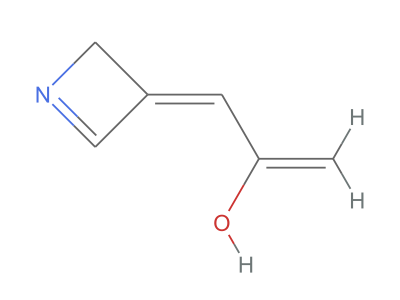

```mathematica
MoleculePlot@RandomChoice@list2
```

```mathematica
BondCount[#,IncludeHydrogens->False]&/@list1//Counts
```

<|7→2538,8→12359,9→21024,10→14411,11→3040|>

```mathematica
Options[Surge]
```

{GeneratedAssetLocation:>Automatic,Asynchronous→True,BondCount→Automatic,Length3CycleCount→Automatic,Length4CycleCount→Automatic,Length3CycleCount→Automatic,DisallowOddLengthCycles→False,DisallowTripleBonds→False,RequirePlanarity→False,MaxDegree→4,MaxCoordinationNumber→4,ExtraCommands→{}}

```mathematica
isomers=GenerateIsomers["C14H24O2","Part"->"7/10"]
```

IsomerResultObject[…]

```mathematica
Dynamic[ProcessStatus@%75]
```

```mathematica
%75
```

IsomerResultObject[…]

```mathematica
smiles=%75["SMILES"];//absoluteTiming
```

```mathematica
stream=OpenRead["/Users/jasonb/Documents/Wolfram/IsomerGeneration/C14H24O2_0ffd95db-ad3a-4c9c-9e1f-e36cf970f66e/C14H24O2.smi"]
```

InputStream[…]

```mathematica
Read[stream,String]
```

COC(=C(C)CC(C)(O)C)C(C1=CC1)(C)C

```mathematica
Skip[stream,String,500]
```

```mathematica
res=CreateDataStructure["DynamicArray"];
Do[Skip[stream,String,RandomInteger[10^6]];res["Append",Read[stream,String]],200]
```

```mathematica
Normal[res]
```

```mathematica
?WordCloud
```

```mathematica
SeedRandom[42];WordCloud[Flatten[{1->ChemicalFormula["C14H24O2"],Thread[.99->MoleculePlot/@RandomSample[,10]]}]]
```

-Graphics-

List all isomers of dichloropentane:

```mathematica
IsomerSmiles["C5H10Cl2"]
```

{ClCCC(C)(Cl)C,CCCC(C)(Cl)Cl,ClC(Cl)C(C)(C)C,CC(Cl)C(C)(Cl)C,CC(C)C(C)(Cl)Cl,CC(Cl)CC(Cl)C,CC(C)CC(Cl)Cl,ClC(CC)(Cl)CC,CC(CC)(Cl)CCl,CC(CCl)(C)CCl,ClC(Cl)CCCC,CC(Cl)CCCCl,ClCCC(Cl)CC,ClCCC(C)CCl,CCCC(Cl)CCl,ClC(Cl)C(C)CC,CC(Cl)C(Cl)CC,CC(Cl)C(C)CCl,CC(C)C(Cl)CCl,CCC(CCl)CCl,ClCCCCCCl}

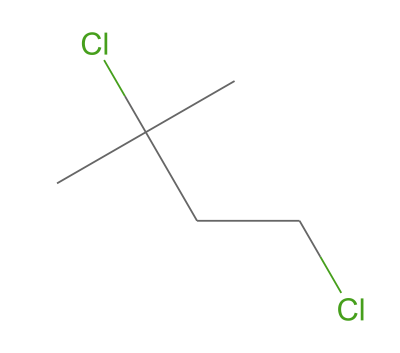
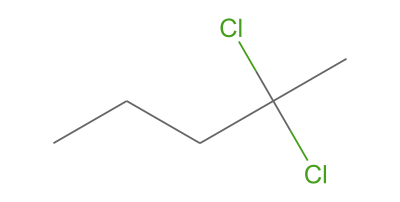
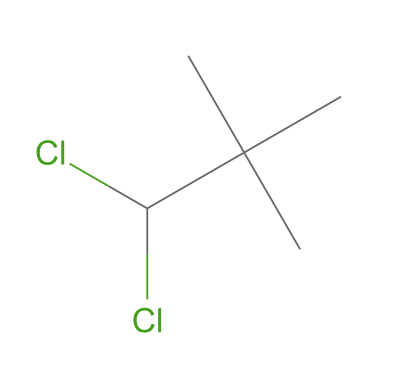
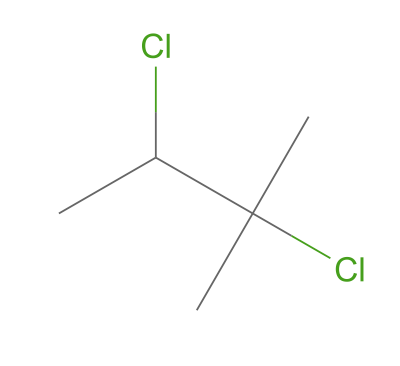
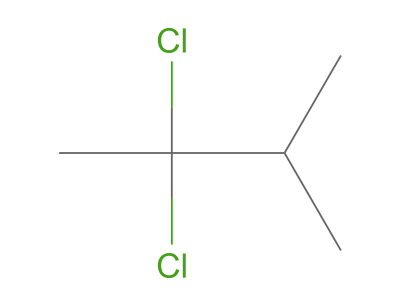
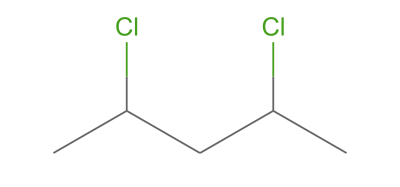
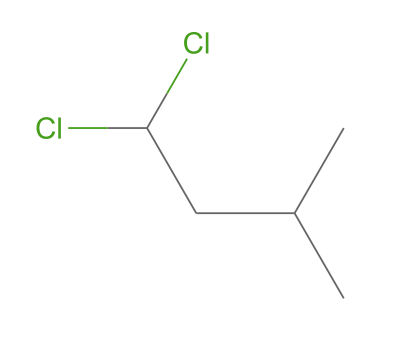
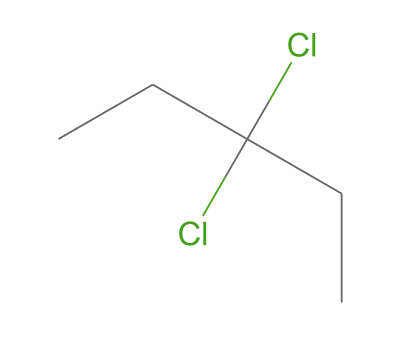

```mathematica
MoleculePlot/@%
```

```mathematica
GenerateIsomers["C3H5Cl"]
```

$Aborted

```mathematica
$ContextPath
```

{WolframChemistry`IsomerGeneration`,Init`,System`,Global`}

```mathematica
iso=Isomers[File["/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H5Cl_2638be98324bad14"]];
```

```mathematica
iso
```

isomers

```mathematica
WolframChemistry`IsomerGeneration`Private`getData[iso]//absoluteTiming
```

{69. μs,<|Method→surge,OutputDirectory→/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H5Cl_2638be98324bad14,Formula→C3H5Cl,CommandLine→{-S,-d4,-c4,C3H5Cl},StartTime→Wed 24 Aug 2022 13:50:56GMT-5,Output→{C3ClH5  H=5 C=3 Cl=1  nv=4 edges=3-4 DBE=1 maxd=4 maxc=4,>Z wrote 4 -> 3 -> 4 in 0.00 sec},Status→Finished,IsomerCount→4,EndTime→Wed 24 Aug 2022 13:50:56GMT-5,Duration→0 s|>}

```mathematica
ToString[Head[iso["Formula"]]]
```

Isomers[File[/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H5Cl_2638be98324bad14]]

```mathematica
WolframChemistry`IsomerGeneration`Private`isomerSubvalue
```

```mathematica
f=File["/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H5Cl_2638be98324bad14"]
```

File[/Users/jasonb/Documents/Wolfram/IsomerGeneration/C3H5Cl_2638be98324bad14]

```mathematica
WolframChemistry`IsomerGeneration`Private`checkData[f]
```

```mathematica
pd@Isomers
```

```mathematica
iso//Information
```

Isomers

```mathematica
Isomers[File@"/Users/jasonb/Desktop/bottcher"]
```

Failure[…]

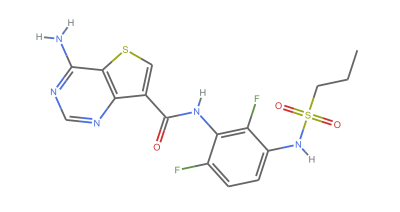

```mathematica
randomMolecule[]//MoleculePlot
```

```mathematica
GenerateIsomers["C14H21Cl",Asynchronous->False]
```

Isomers[…]

```mathematica
?Skip
```

```mathematica
Skip[%2,10^6]
```

```mathematica
ReadList[%2,Molecule,10]
```

{Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…],Molecule[…]}

```mathematica
Information@%
```

Isomers

```mathematica
Read[%84]
```

CC(C#CC(C)(C)C)(Cl)CC(C#C)(C)C

```mathematica
ReadList[%][[-5;;]]
```

ReadList::stream: … is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Part::take: Cannot take positions -5 through -1 in ….

ReadList[Isomers[…]]⟦-5;;All⟧

```mathematica
DeleteFile@%
```

```mathematica
%
```

Isomers[…]

```mathematica
p=%["Process"]
```

ProcessObject[…]

```mathematica
ProcessInformation[p]
```

<|ExitCode→None|>

```mathematica
KillProcess[p]
```

```mathematica
Isomers[…] //KillProcess
```

```mathematica
Isomers[…]
```

Isomers[…]

```mathematica
%
```

```mathematica
Isomers[…]
```

Isomers[…]

```mathematica
KillProcess@%
```

```mathematica
Isomers[…]
```

Isomers[…]

```mathematica
FileSize@%
```

0.503722 GB

```mathematica
KillProcess@%%
```

```mathematica
FindFile["WolframChemistry`IsomerGeneration`"]
```

/Users/jasonb/WolframWorkspaces/Published_Paclets/IsomerGeneration/IsomerGeneration/Kernel/IsomerGeneration.wl

```mathematica
OpenWrite
```

```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Inherited]
```

```mathematica
Quit
```

g has been cleared

```mathematica
$HistoryLength
```

∞

```mathematica
list=Range[10^8];
```

```mathematica
foo=<|"a":>Print[2]|>
```

<|a:>Print[2]|>

```mathematica
foo["a"]=.
```

```mathematica
%
```

```mathematica
(1;2; )
```

```mathematica
%
```

2

```mathematica
KeyDropFrom[foo,"a"]
```

<||>